Import

```mathematica
ElectronILLData225WFilter=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronILLData_22,5°WFilter_Xm20p05_32Bins.txt","Table"];ElectronILLData90WFilter=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/Electron_ILL90WFilter_Xm55p05_32Bins.txt","Table"];
ElectronILLData180WFilter=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronILLData_180°WFilter_Xm85p05_32Bins.txt","Table"];
```

```mathematica
ProtonILLData225WFilter=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ProtonILLData_22,5°WFilter_Xm20p05_32Bins.txt","Table"];ProtonILLData90WFilter=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ProtonILLData_90WFilter_Xm55p05_48Bins.txt","Table"];
ProtonILLData180WFilter=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ProtonILLData_180WFilter_Xm85p05_32Bins.txt","Table"];
```

### PERC data

```mathematica
ElectronPERCData180=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronPERCData_180°_Xm70p05_32Bins.txt","Table"];
ElectronPERCData180b1em3=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronPERCData_180°_Xm70p05_32Bins_b1e-3.txt","Table"];
ProtonPERCData180=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ProtonPERCData_180°_Xm70p05_32Bins.txt","Table"];
ProtonPERCData180a3em3=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ProtonPERCData_180°_Xm70p05_32Bins_da3e-3.txt","Table"];
```

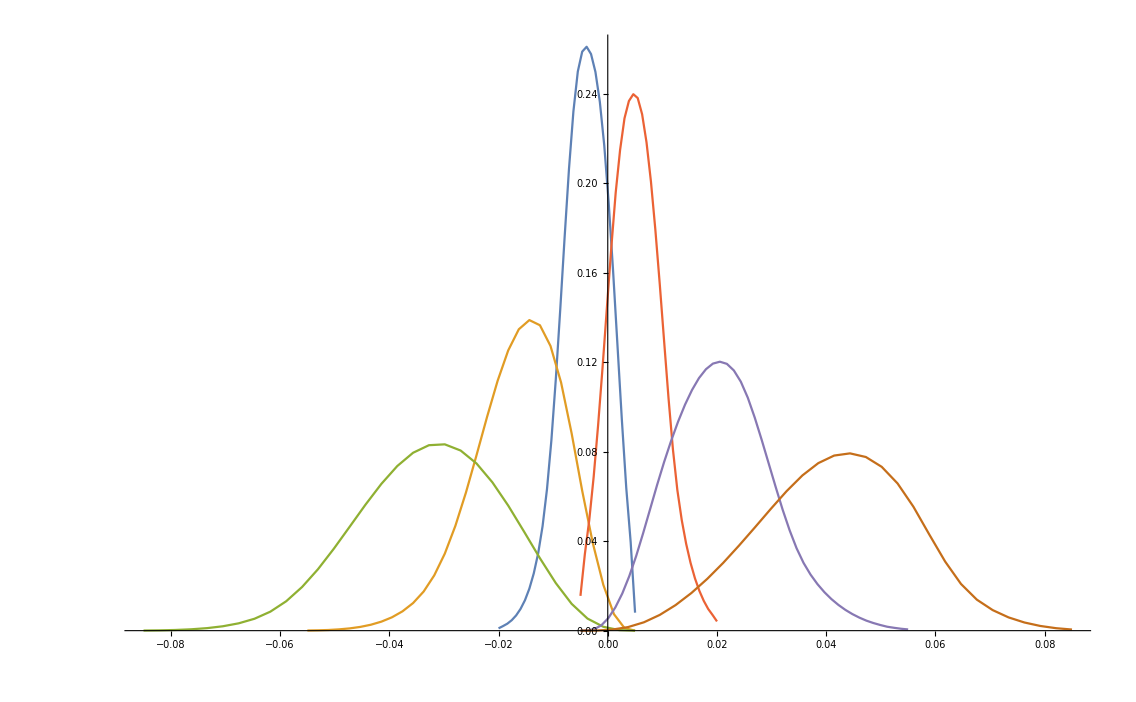

```mathematica
ListLinePlot[
{
#*{1,9/2.5}&/@ElectronILLData225WFilter,
#*{1,9/6}&/@ElectronILLData90WFilter,
ElectronILLData180WFilter,
#*{1,9/2.5}&/@ProtonILLData225WFilter,
#*{1,9*48/6/32}&/@ProtonILLData90WFilter,
ProtonILLData180WFilter
}]
```

Drift Spectra Plotting

```mathematica
DataList={
#*{1,9/2.5}&/@ElectronILLData225WFilter,
#*{1,9/6}&/@ElectronILLData90WFilter,
ElectronILLData180WFilter,
#*{1,9/2.5}&/@ProtonILLData225WFilter,
#*{1,9*48/6/32}&/@ProtonILLData90WFilter,
ProtonILLData180WFilter
};
```

```mathematica
shadowbox[legend_]:=Graphics[{{White,EdgeForm[Black],Rectangle[{-0.7,-0.4},{0.7,0.4}]},Inset[legend,{0.,0.},Center]},ImageSize->{150,130}]
```

### we want to compare with same bin-density, so we have to rescale most of them -.-

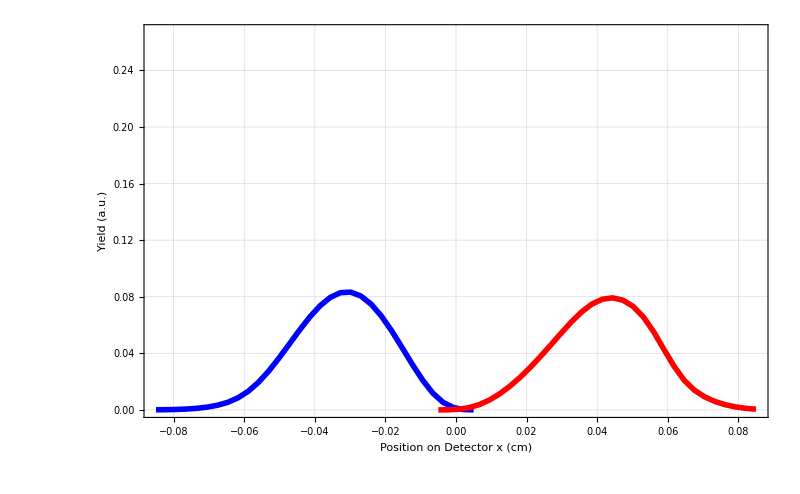

```mathematica
ElectronProtonComparePlot=ListLinePlot[
DataList[[{3,6}]],

GridLines->Automatic,GridLinesStyle->Directive[Thickness[0.002],Black],Frame->True,BaseStyle->25,FrameLabel->{{"Yield (a.u.)",None},{"Position on Detector x (cm)","Drift Distance Spectra, α=180°"}},ImageSize->{800,600},PlotStyle->{Directive[Thickness[0.005],Blue],Directive[Thickness[0.005],Red]},ImagePadding->{{90,10},{80,40}},

PlotLegends->
Placed[
LineLegend[{"e^-","p^+"},LabelStyle->25,LegendFunction->shadowbox,LegendMarkerSize->{30,20},LegendMarkers->{Graphics[{Thickness[0.3],Line[{{0,0},{3,0}}]}],Graphics[{Thickness[0.3],Line[{{0,0},{3,0}}]}]}],
{0.8,0.87}],

(*FrameTicks->{
{Join[Table[{y,y,{0.02,0.},Thick},{y,0,0.08,0.02}],Table[{y,"",{0.01,0.},Thick},{y,0,0.08,0.005}]],None},
{Join[Table[{y,y,{0.02,0.},Thick},{y,0,9,2}],Table[{y,"",{0.01,0.},Thick},{y,0,9,0.5}]],None}
},*)

FrameStyle->Directive[Black,Thick],PlotRangePadding->{{0.001,0.001},{0,0.001}},PlotRange->{{-0.085,0.085},{0,0.267}}]
```

```mathematica
Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronProtonCompare_wFilter_180°.svg",ElectronProtonComparePlot];
```

Including residual

```mathematica
shadowbox[legend_]:=Graphics[{{White,EdgeForm[Black],Rectangle[{-0.7,-0.4},{0.7,0.4}]},Inset[legend,{0.,0.},Center]},ImageSize->{150,130}]
```

```mathematica
shadowbox2[legend_]:=Graphics[{{White,EdgeForm[Black],Rectangle[{-1.2,-0.4},{1.2,0.4}]},Inset[legend,{0.,0.},Center]},ImageSize->{270,130}]
```

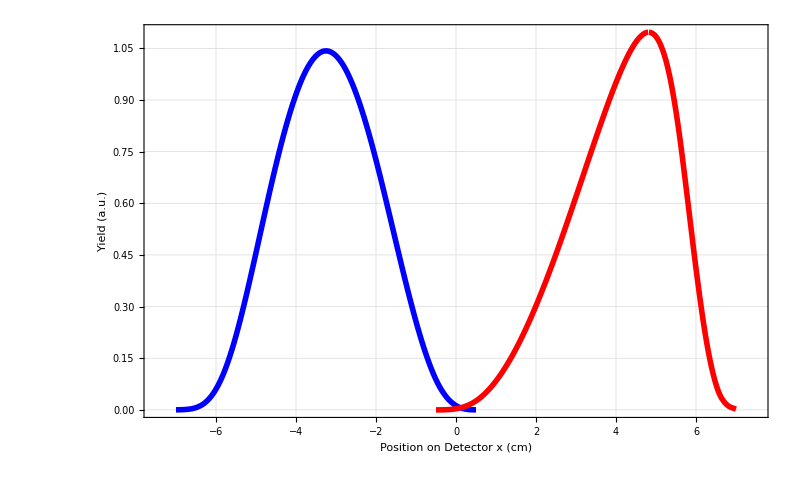

```mathematica
SpectraPlot=ListLinePlot[
{
{100,1/0.07}*#&/@ElectronPERCData180,
{100,1/0.07}*#&/@ProtonPERCData180
},

GridLines->Automatic,GridLinesStyle->Directive[Thickness[0.002],Black],Frame->True,BaseStyle->25,FrameLabel->{{"Yield (a.u.)",None},{"Position on Detector x (cm)","Drift Distance Spectra at PERC, α=180°"}},ImageSize->{800,500},PlotStyle->{Directive[Thickness[0.005],Blue],Directive[Thickness[0.005],Red]},ImagePadding->{{110,10},{8,40}},InterpolationOrder->2,

PlotLegends->
Placed[
LineLegend[{"e^-","p^+"},LabelStyle->25,LegendFunction->shadowbox,LegendMarkerSize->{30,20},LegendMarkers->{Graphics[{Thickness[0.3],Line[{{0,0},{3,0}}]}],Graphics[{Thickness[0.3],Line[{{0,0},{3,0}}]}]}],
{0.55,0.87}],

(*FrameTicks->{
{Join[Table[{y,y,{0.02,0.},Thick},{y,0,0.08,0.02}],Table[{y,"",{0.01,0.},Thick},{y,0,0.08,0.005}]],None},
{Join[Table[{y,y,{0.02,0.},Thick},{y,0,9,2}],Table[{y,"",{0.01,0.},Thick},{y,0,9,0.5}]],None}
},*)

FrameStyle->Directive[25,Bold,Black],PlotRangePadding->{{0.001,0.001},{0,0.01}},PlotRange->{{-7.5,7.5},Automatic}]
```

```mathematica
1.1/Sin[45/180*Pi]
```

1.55563

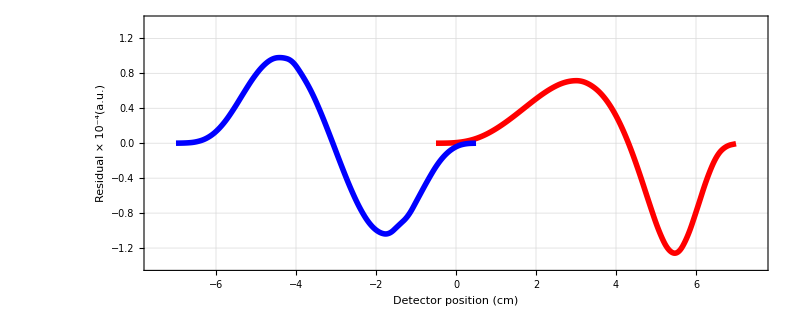

```mathematica
residualplot=ListLinePlot[
{
Transpose[{ProtonPERCData180[[All,1]]*100,(ProtonPERCData180[[All,2]]-ProtonPERCData180a3em3[[All,2]])*10^4/0.07}],
Transpose[{ElectronPERCData180[[All,1]]*100,(ElectronPERCData180[[All,2]]-ElectronPERCData180b1em3[[All,2]])*10^4/0.07}]
},
Frame->True,GridLines->Automatic,PlotStyle->{Directive[Thickness[0.005],Red],Directive[Thickness[0.005],Blue]},InterpolationOrder->2,FrameStyle->Directive[25,Bold,Black],FrameLabel->{{"Residual × 10^-4(a.u.)",None},{"Detector position (cm)",None}},

PlotLegends->Placed[LineLegend[{"p+, Δa/a=3×10^-3","e-, Δb=1×10^-3"},LegendFunction->(shadowbox2[#]&),LabelStyle->Directive[25,Bold],LegendMarkers->{Graphics[{Thickness[0.3],Line[{{0,0},{3,0}}]}],Graphics[{Thickness[0.3],Line[{{0,0},{3,0}}]}]}],{0.455,0.83}],

ImageSize->800,PlotRange->{{-7.5,7.5},{-1.4,1.4}},AspectRatio->1/2.5,ImagePadding->{{110,10},{80,1}}]
```

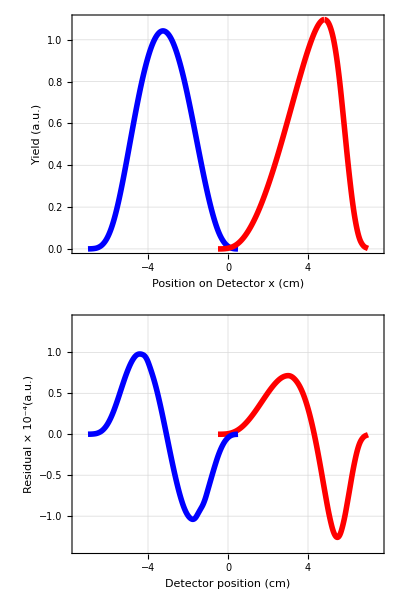

```mathematica
SpectraAndResidualPlot=Column[{SpectraPlot,residualplot}]
```

```mathematica
Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/AtPERC180_SpectraAndResidual.png",SpectraAndResidualPlot];
```

ItemAspectRatio::shdw: Symbol ItemAspectRatio appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.